```mathematica
csols=Solve[x^2+c+.001/x^2==x,x,Reals];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
iterNum= 100000;
minX = -.22;
maxX= -.063;
scaleIter = (maxX-minX)/iterNum;
betaVal = .001;
d = 2;
n = 2;
critR = .001^(1/(2+2));
tab = {};
Parallelize[
For[i = 0, i < iterNum, i++,
	cVal = maxX - scaleIter*i;
	codStr = "";
	xVal = critR//N;
	row = {};
	For[j = 0, j < 20, j++,
		If[xVal > critR,
			fVal = x/.csols[[2]]/.c->cVal//N;
			If[!NumericQ[fVal],
				(*Then we do not have a right fixed point*)
				fVal = -Infinity;
			];
			(* 
				Since fval was solved for over the reals, if we get to this point and 
				there is any complex portion, it MUST be numerical error. Thus we 
				can safely ignore it.
			*)
			If[xVal < Re[fVal],
				(*codStr = codStr<>" F, "*)
				AppendTo[row,"F"];,
				AppendTo[row,"R"];];,
			If[xVal == critR,
				AppendTo[row,"C"];,
				If[xVal > 0 && xVal < critR,
					AppendTo[row,"L"];,
					If[xVal < 0 && xVal > -critR,
						AppendTo[row,"r"];,
						If[xVal < 0 && xVal < -critR,
							AppendTo[row,"l"];
						];
					];
				];
			];
		];
		xVal = xVal^2 + cVal + .001/(xVal^2);
	];
	AppendTo[row,cVal];
	AppendTo[tab,row];
];];
```

```mathematica
Export["~/codings.csv", tab]
```

~/codings.csv

```mathematica
sf = D[singpert[x,c,beta],{x,3}]/D[singpert[x,c,beta],{x,2}] - (3/2)(D[singpert[x,c,beta],{x,2}]/D[singpert[x,c,beta],x])^2
```

-(24 beta)/((2+(6 beta)/x^4) x^5)-(3 (2+(6 beta)/x^4)^2)/(2 (-(2 beta)/x^3+2 x)^2)

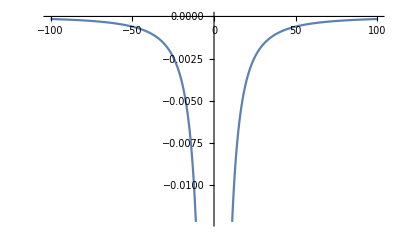

```mathematica
Plot[sf/.{c->-10,beta->.1},{x,-100,100}]
```

```mathematica
scaleIter
```

0.000045

```mathematica
tab
```

{{C,L,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,-0.063},{C,L,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,-0.0630016},{C,L,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,-0.0630031},{C,L,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,R,-0.0630047},99993,{C,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,-0.219995},{C,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,-0.219997},{C,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,r,-0.219998}}
 |  |  |  |